```mathematica
a[n_]:=(-1)^Floor[n/Log[n]] 1/n;
```

```mathematica
an=Table[a[n],{n,5,50000}];
```

```mathematica
lst={10,20,30,50,80,100,150,200,250,300,400,500,800,1000,1500,2000,3000,5000,8000,10000,15000,20000,30000,50000};
```

```mathematica
Length[lst]
```

24

```mathematica
Table[NMaximize[{∑_(k=5)^lst[[s]] (a[k]Sin[k x]),0<x<1},x],{s,Length[lst]}]
```

{{0.589058,{x→0.775929}},{1.02363,{x→0.753982}},{1.20745,{x→0.732105}},{1.37992,{x→0.712354}},{1.28421,{x→0.727231}},{1.29281,{x→0.705568}},{1.28329,{x→0.71251}},{1.27504,{x→0.716855}},{1.28036,{x→0.707593}},{1.28444,{x→0.709305}},{1.29352,{x→0.712656}},{1.30775,{x→0.709905}},{1.29849,{x→0.708529}},{1.29779,{x→0.708446}},{1.29727,{x→0.709257}},{1.29883,{x→0.709753}},{1.2985,{x→0.709279}},{1.30068,{x→0.709452}},{1.3008,{x→0.709521}},{1.30017,{x→0.709528}},{1.3004,{x→0.709607}},{1.30041,{x→0.70963}},{1.30101,{x→0.709541}},{1.30163,{x→0.709256}}}

```mathematica
%//MatrixForm
```

(0.589058 | {x→0.775929}
1.02363 | {x→0.753982}
1.20745 | {x→0.732105}
1.37992 | {x→0.712354}
1.28421 | {x→0.727231}
1.29281 | {x→0.705568}
1.28329 | {x→0.71251}
1.27504 | {x→0.716855}
1.28036 | {x→0.707593}
1.28444 | {x→0.709305}
1.29352 | {x→0.712656}
1.30775 | {x→0.709905}
1.29849 | {x→0.708529}
1.29779 | {x→0.708446}
1.29727 | {x→0.709257}
1.29883 | {x→0.709753}
1.2985 | {x→0.709279}
1.30068 | {x→0.709452}
1.3008 | {x→0.709521}
1.30017 | {x→0.709528}
1.3004 | {x→0.709607}
1.30041 | {x→0.70963}
1.30101 | {x→0.709541}
1.30163 | {x→0.709256})

```mathematica
Manipulate[tbl=Table[∑_(k=5)^lst[[n]] (a[k]Sin[k x]),{n,s,s+1}];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]],{s,1,Length[lst]-1,1}]
```

```mathematica
tbl=Table[∑_(k=5)^lst[[n]] (a[k]Sin[k x]),{n,Length[lst]}];
```

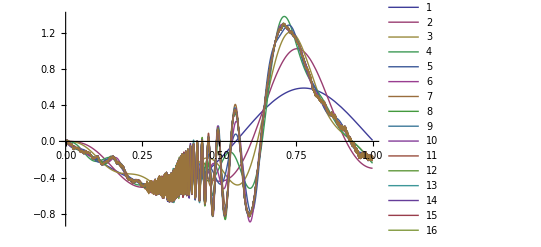

```mathematica
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
```

```mathematica
Log[50000]/Log[2]//N
```

15.6096

```mathematica
tbl=Table[∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),{n,2,15}];
```

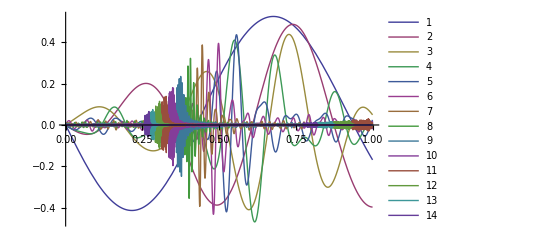

```mathematica
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
```

```mathematica
Table[NMaximize[{∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),0<x<1},x],{n,2,15}]
```

{{0.523998,{x→0.676758}},{0.485782,{x→0.740268}},{0.437226,{x→0.727562}},{0.409572,{x→0.550216}},{0.435726,{x→0.556623}},{0.394133,{x→0.498064}},{0.386655,{x→0.445189}},{0.322283,{x→0.406716}},{0.234508,{x→0.374884}},{0.178731,{x→0.35099}},{0.148427,{x→0.327307}},{0.0926036,{x→0.29274}},{0.0746324,{x→0.283614}},{0.0600311,{x→0.269784}}}

```mathematica
%//MatrixForm
```

(0.523998 | {x→0.676758}
0.485782 | {x→0.740268}
0.437226 | {x→0.727562}
0.409572 | {x→0.550216}
0.435726 | {x→0.556623}
0.394133 | {x→0.498064}
0.386655 | {x→0.445189}
0.322283 | {x→0.406716}
0.234508 | {x→0.374884}
0.178731 | {x→0.35099}
0.148427 | {x→0.327307}
0.0926036 | {x→0.29274}
0.0746324 | {x→0.283614}
0.0600311 | {x→0.269784})

```mathematica
cnvrgnclst=%;
```

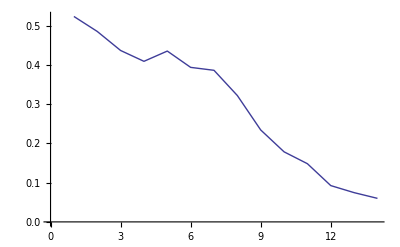

```mathematica
ListLinePlot[Map[First,cnvrgnclst]]
```

```mathematica
a[n_]:=(-1)^Floor[(Log[n]/Log[2]+1/2)Log[Log[n]]-Log[n] Log[Log[2]]/Log[2]-Log[n]/Log[2]];
```

```mathematica
an=Table[a[n],{n,6,50000}];
```

```mathematica
Export["C:\\Documents and Settings\\Administrator\\桌面\\an.txt",an]
```

C:\Documents and Settings\Administrator\桌面\an.txt

```mathematica
∑_(k=6)^lst[[1]] (an[[k-5]] 1/k Sin[k x])
```

1/6 Sin[6 x]+1/7 Sin[7 x]+1/8 Sin[8 x]+1/9 Sin[9 x]-1/10 Sin[10 x]

```mathematica
Table[NMaximize[{∑_(k=6)^lst[[s]] (an[[k-5]] 1/k Sin[k x]),0<x<1},x],{s,Length[lst]}]
```

{{0.449992,{x→0.233419}},{0.684864,{x→0.379833}},{0.957873,{x→0.380484}},{1.00841,{x→0.353174}},{0.93629,{x→0.342469}},{0.942357,{x→0.394255}},{0.952166,{x→0.37353}},{0.913519,{x→0.395247}},{0.905899,{x→0.393594}},{0.913396,{x→0.393496}},{0.969799,{x→0.358328}},{0.98,{x→0.358437}},{0.932064,{x→0.391185}},{0.931216,{x→0.390575}},{0.935472,{x→0.391212}},{0.993897,{x→0.357152}},{0.996685,{x→0.357892}},{0.997768,{x→0.357972}},{0.998355,{x→0.358}},{0.998791,{x→0.357951}},{0.998234,{x→0.357965}},{0.998176,{x→0.357945}},{0.998477,{x→0.357914}},{0.998748,{x→0.357929}}}

```mathematica
%//MatrixForm
```

(0.449992 | {x→0.233419}
0.684864 | {x→0.379833}
0.957873 | {x→0.380484}
1.00841 | {x→0.353174}
0.93629 | {x→0.342469}
0.942357 | {x→0.394255}
0.952166 | {x→0.37353}
0.913519 | {x→0.395247}
0.905899 | {x→0.393594}
0.913396 | {x→0.393496}
0.969799 | {x→0.358328}
0.98 | {x→0.358437}
0.932064 | {x→0.391185}
0.931216 | {x→0.390575}
0.935472 | {x→0.391212}
0.993897 | {x→0.357152}
0.996685 | {x→0.357892}
0.997768 | {x→0.357972}
0.998355 | {x→0.358}
0.998791 | {x→0.357951}
0.998234 | {x→0.357965}
0.998176 | {x→0.357945}
0.998477 | {x→0.357914}
0.998748 | {x→0.357929})

```mathematica
tbl=Table[∑_(k=6)^lst[[n]] (an[[k-5]] 1/k Sin[k x]),{n,Length[lst]}];
```

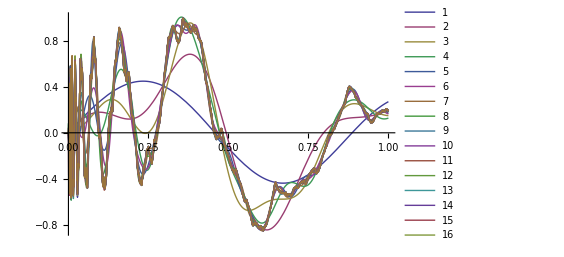

```mathematica
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
```

```mathematica
tbl=Table[∑_(k=2^n)^(2^(n+1)) (an[[k-5]] 1/k Sin[k x]),{n,3,14}];
```

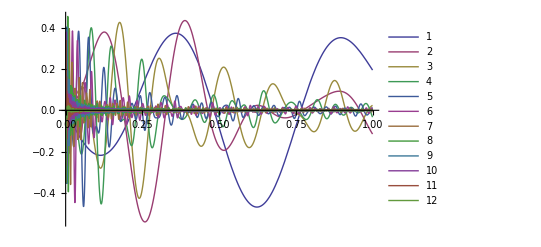

```mathematica
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
```

```mathematica
Table[NMaximize[{∑_(k=2^n)^(2^(n+1)) (an[[k-5]]Sin[k x]),0<x<1},x],{n,3,14}]
```

{{4.49226,{x→0.366829}},{10.3292,{x→0.383405}},{20.4526,{x→0.177039}},{37.7052,{x→0.0844745}},{73.1347,{x→0.0427628}},{150.698,{x→0.0224483}},{306.908,{x→0.0119128}},{678.851,{x→0.00691994}},{467.053,{x→0.000391252}},{2527.08,{x→0.00220905}},{4115.56,{x→0.000743435}},{10972.3,{x→0.000460078}}}

```mathematica
%//MatrixForm
```

(4.49226 | {x→0.366829}
10.3292 | {x→0.383405}
20.4526 | {x→0.177039}
37.7052 | {x→0.0844745}
73.1347 | {x→0.0427628}
150.698 | {x→0.0224483}
306.908 | {x→0.0119128}
678.851 | {x→0.00691994}
467.053 | {x→0.000391252}
2527.08 | {x→0.00220905}
4115.56 | {x→0.000743435}
10972.3 | {x→0.000460078})

```mathematica
a[n_]:=(-1)^Floor[(Log[n])^2] 1/n;
```

```mathematica
an=Table[a[n],{n,5,50000}];
```

```mathematica
lst={10,20,30,50,80,100,150,200,250,300,400,500,800,1000,1500,2000,3000,5000,8000,10000,15000,20000,30000,50000};
```

```mathematica
Length[lst]
```

24

```mathematica
Table[NMaximize[{∑_(k=5)^lst[[s]] (a[k]Sin[k x]),0<x<1},x],{s,Length[lst]}]
```

{{0.113322,{x→0.837758}},{0.226117,{x→0.0892578}},{0.358054,{x→0.781704}},{0.454837,{x→0.764466}},{0.469996,{x→0.579223}},{0.494634,{x→0.574787}},{0.511037,{x→0.577244}},{0.561927,{x→0.574653}},{0.547665,{x→0.57426}},{0.555663,{x→0.57291}},{0.479565,{x→0.790196}},{0.567822,{x→0.57132}},{0.559552,{x→0.569735}},{0.56347,{x→0.57068}},{0.569225,{x→0.570237}},{0.568824,{x→0.570158}},{0.569784,{x→0.569793}},{0.547817,{x→0.575826}},{0.574901,{x→0.569769}},{0.574427,{x→0.569762}},{0.575043,{x→0.569856}},{0.57509,{x→0.56982}},{0.574836,{x→0.569858}},{0.574852,{x→0.569745}}}

```mathematica
%//MatrixForm
```

(0.113322 | {x→0.837758}
0.226117 | {x→0.0892578}
0.358054 | {x→0.781704}
0.454837 | {x→0.764466}
0.469996 | {x→0.579223}
0.494634 | {x→0.574787}
0.511037 | {x→0.577244}
0.561927 | {x→0.574653}
0.547665 | {x→0.57426}
0.555663 | {x→0.57291}
0.479565 | {x→0.790196}
0.567822 | {x→0.57132}
0.559552 | {x→0.569735}
0.56347 | {x→0.57068}
0.569225 | {x→0.570237}
0.568824 | {x→0.570158}
0.569784 | {x→0.569793}
0.547817 | {x→0.575826}
0.574901 | {x→0.569769}
0.574427 | {x→0.569762}
0.575043 | {x→0.569856}
0.57509 | {x→0.56982}
0.574836 | {x→0.569858}
0.574852 | {x→0.569745})

```mathematica
tbl=Table[∑_(k=5)^lst[[n]] (a[k]Sin[k x]),{n,Length[lst]}];
```

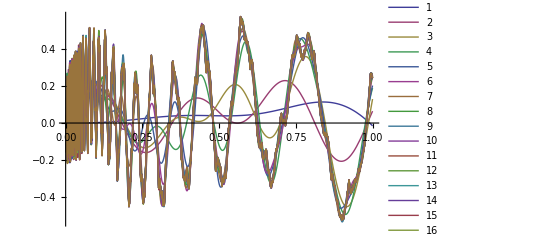

```mathematica
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
```

```mathematica
tbl=Table[∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),{n,2,15}];
```

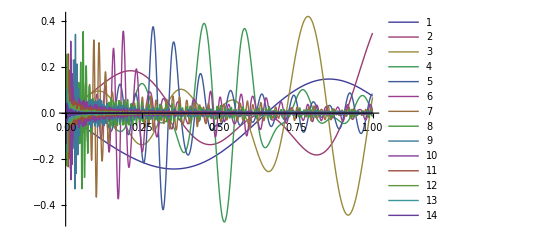

```mathematica
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
```

```mathematica
Table[NMaximize[{∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),0<x<1},x],{n,2,15}]
```

{{0.147946,{x→0.858049}},{0.347776,{x→1.}},{0.419838,{x→0.789664}},{0.389662,{x→0.451122}},{0.375036,{x→0.284949}},{0.0734266,{x→0.609403}},{0.317867,{x→0.0920042}},{0.354055,{x→0.0570351}},{0.216006,{x→0.0370522}},{0.314483,{x→0.0166009}},{0.18727,{x→0.00818298}},{0.259683,{x→0.00522961}},{0.24399,{x→0.00281275}},{0.242721,{x→0.00158035}}}

```mathematica
%//MatrixForm
```

(0.147946 | {x→0.858049}
0.347776 | {x→1.}
0.419838 | {x→0.789664}
0.389662 | {x→0.451122}
0.375036 | {x→0.284949}
0.0734266 | {x→0.609403}
0.317867 | {x→0.0920042}
0.354055 | {x→0.0570351}
0.216006 | {x→0.0370522}
0.314483 | {x→0.0166009}
0.18727 | {x→0.00818298}
0.259683 | {x→0.00522961}
0.24399 | {x→0.00281275}
0.242721 | {x→0.00158035})

```mathematica
cnvrgnclst=%;
```

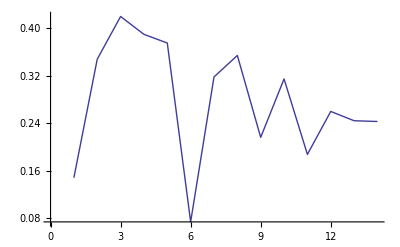

```mathematica
ListLinePlot[Map[First,cnvrgnclst]]
```

```mathematica
n=16;
NMaximize[{∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),0<x<1},x]
Clear[n]
```

{0.189734,{x→0.000701878}}

```mathematica
Table[N[Total[Abs[Differences[Table[a[k],{k,2^m,2^(m+1)}]]]]],{m,1,16}]
```

{0.916667,1.10833,0.5625,0.461397,0.225629,0.139578,0.0829047,0.0479091,0.029041,0.0140961,0.00778656,0.00425363,0.00230209,0.00123637,0.000629141,0.000365323}

```mathematica
Table[N[1/2^m Total[Table[Abs[a[k]],{k,2^m,2^(m+1)}]]],{m,1,16}]
```

{0.541667,0.221131,0.098484,0.0462666,0.0223952,0.0110138,0.00546102,0.00271905,0.00135666,0.000677617,0.00033863,0.00016927,0.0000846239,0.0000423091,0.0000211539,0.0000105768}

```mathematica
%21/%23
```

{1.69231,5.01211,5.71159,9.97257,10.0749,12.673,15.1812,17.6198,21.4062,20.8025,22.9943,25.1292,27.2038,29.2224,29.7412,34.5402}

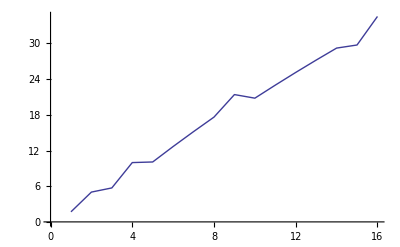

```mathematica
ListLinePlot[%26]
```

...........................................................

...........................................................

...........................................................

«1 more identical outputs»

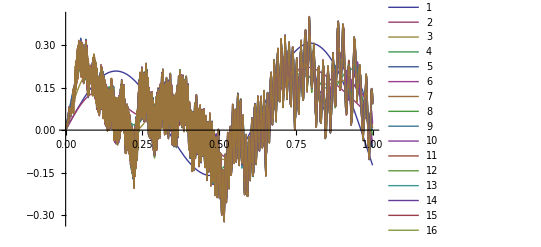

...........................................................

...........................................................

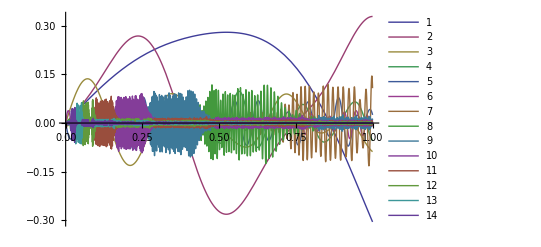

...........................................................

...........................................................

(0.279682 | {x→0.523599}
0.328401 | {x→1.}
0.136317 | {x→0.0711772}
0.0652458 | {x→0.942213}
0.0779343 | {x→0.889167}
0.0382421 | {x→0.00866641}
0.145107 | {x→0.997689}
0.116586 | {x→0.657495}
0.0945601 | {x→0.336959}
0.0826701 | {x→0.202109}
0.0718809 | {x→0.13061}
0.0648731 | {x→0.0735737}
0.0680381 | {x→0.0503323}
0.0590578 | {x→0.0266771})

...........................................................

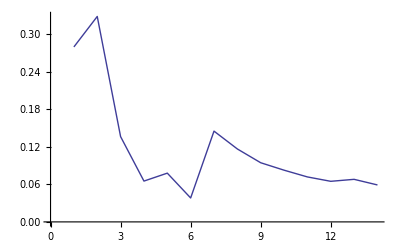

...........................................................

...........................................................

...........................................................

{2.61538,3.20323,5.39679,22.2219,54.6685,86.8358,113.988,147.886,187.259,226.317,272.31,322.396,376.577,434.867,498.711,562.342}

...........................................................

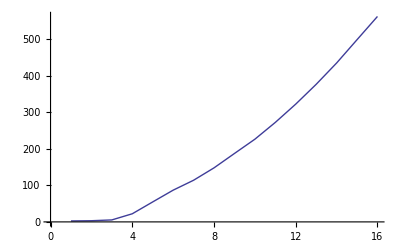

...........................................................

```mathematica
a[n_]:=(-1)^Floor[(Log[n])^3] 1/n;
Print["..........................................................."];
an=Table[a[n],{n,5,50000}];
Print["..........................................................."];
lst={10,20,30,50,80,100,150,200,250,300,400,500,800,1000,1500,2000,3000,5000,8000,10000,15000,20000,30000,50000};
Print["..........................................................."];
tbl=Table[∑_(k=5)^lst[[n]] (a[k]Sin[k x]),{n,Length[lst]}];
Print["..........................................................."];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["..........................................................."];
tbl=Table[∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),{n,2,15}];
Print["..........................................................."];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["..........................................................."];
cnvrgnclst=Table[NMaximize[{∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),0<x<1},x],{n,2,15}];
Print["..........................................................."];
cnvrgnclst//MatrixForm
Print["..........................................................."];
ListLinePlot[Map[First,cnvrgnclst]]
Print["..........................................................."];
diff=Table[N[Total[Abs[Differences[Table[a[k],{k,2^m,2^(m+1)}]]]]],{m,1,16}];
Print["..........................................................."];
abs=Table[N[1/2^m Total[Table[Abs[a[k]],{k,2^m,2^(m+1)}]]],{m,1,16}];
Print["..........................................................."];
diff/abs
Print["..........................................................."];
ListLinePlot[diff/abs]
Print["..........................................................."];
```

...........................................................

...........................................................

...........................................................

«1 more identical outputs»

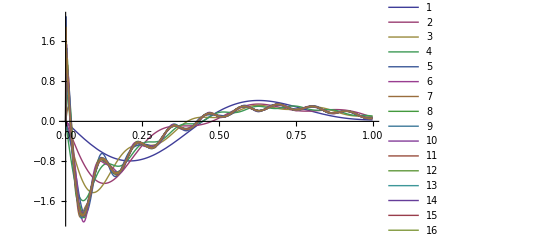

...........................................................

...........................................................

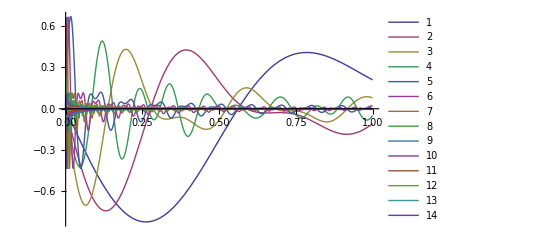

...........................................................

...........................................................

(0.409103 | {x→0.785398}
0.427641 | {x→0.392699}
0.432251 | {x→0.19635}
0.492043 | {x→0.119098}
0.671075 | {x→0.0163625}
0.666003 | {x→0.00818123}
0.115093 | {x→0.0204531}
0.662198 | {x→0.00204531}
0.661563 | {x→0.00102265}
0.661246 | {x→0.000511327}
0.642214 | {x→0.000259499}
0.433785 | {x→0.000383492}
0.433785 | {x→0.000191747}
0.433785 | {x→0.0000958738})

...........................................................

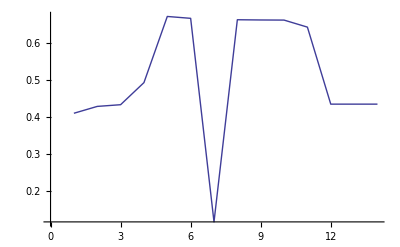

...........................................................

...........................................................

...........................................................

{1.69231,0.565276,0.634621,0.675433,2.32142,0.709339,0.715297,0.71831,0.719826,0.720586,0.720967,2.17913,0.721252,0.7213,0.721324,0.721336}

...........................................................

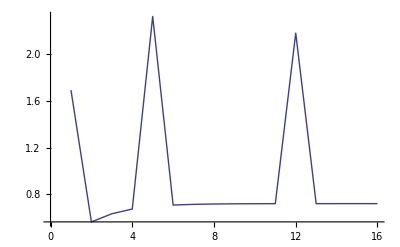

...........................................................

```mathematica
a[n_]:=(-1)^Floor[(Log[n])^(1/2)] 1/n;
Print["..........................................................."];
an=Table[a[n],{n,5,50000}];
Print["..........................................................."];
lst={10,20,30,50,80,100,150,200,250,300,400,500,800,1000,1500,2000,3000,5000,8000,10000,15000,20000,30000,50000};
Print["..........................................................."];
tbl=Table[∑_(k=5)^lst[[n]] (a[k]Sin[k x]),{n,Length[lst]}];
Print["..........................................................."];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["..........................................................."];
tbl=Table[∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),{n,2,15}];
Print["..........................................................."];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["..........................................................."];
cnvrgnclst=Table[NMaximize[{∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),0<x<1},x],{n,2,15}];
Print["..........................................................."];
cnvrgnclst//MatrixForm
Print["..........................................................."];
ListLinePlot[Map[First,cnvrgnclst]]
Print["..........................................................."];
diff=Table[N[Total[Abs[Differences[Table[a[k],{k,2^m,2^(m+1)}]]]]],{m,1,16}];
Print["..........................................................."];
abs=Table[N[1/2^m Total[Table[Abs[a[k]],{k,2^m,2^(m+1)}]]],{m,1,16}];
Print["..........................................................."];
diff/abs
Print["..........................................................."];
ListLinePlot[diff/abs]
Print["..........................................................."];
```

...........................................................a[n]已经算完

...........................................................计算5到n个的部分和

...........................................................5到n个部分和的图像

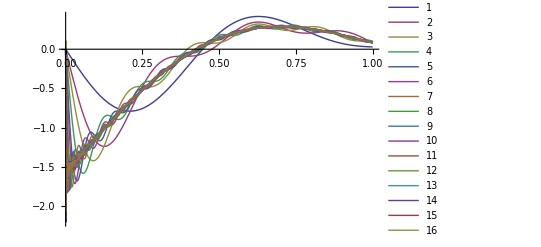

...........................................................cauchy判别

...........................................................cauchy判别图像

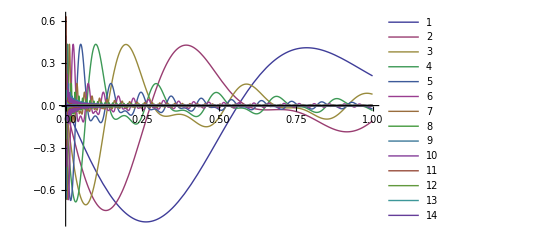

...........................................................截断的最大值

...........................................................截断的最大值列表

(0.409103 | {x→0.785398}
0.427641 | {x→0.392699}
0.432251 | {x→0.19635}
0.433402 | {x→0.0981748}
0.43369 | {x→0.0490874}
0.433762 | {x→0.0245437}
0.433779 | {x→0.0122718}
0.433784 | {x→0.00613592}
0.0679996 | {x→0.0214757}
0.500231 | {x→0.00208577}
0.661088 | {x→0.000255656}
0.661008 | {x→0.000127826}
0.660969 | {x→0.0000639159}
0.660949 | {x→0.0000319517})

...........................................................截断的最大值图像

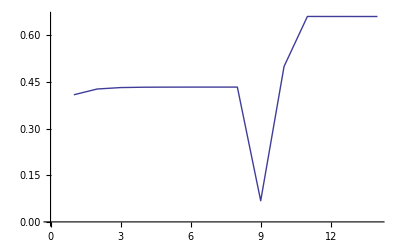

...........................................................LHS

...........................................................RHS

...........................................................LHS/RHS

{1.69231,0.565276,0.634621,0.675433,0.697695,0.709339,0.715297,0.71831,0.719826,0.720586,2.70223,0.721157,0.721252,0.7213,0.721324,0.721336}

...........................................................LHS/RHS的图像

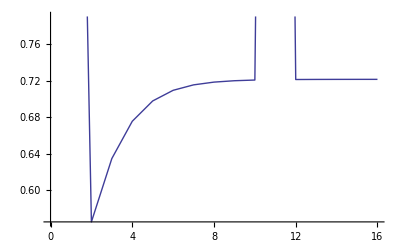

...........................................................另一波(Log[n])^(2/3)

...........................................................a[n]已经算完

...........................................................计算5到n个的部分和

...........................................................5到n个部分和的图像

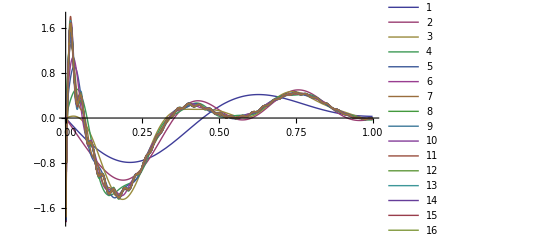

...........................................................cauchy判别

...........................................................cauchy判别图像

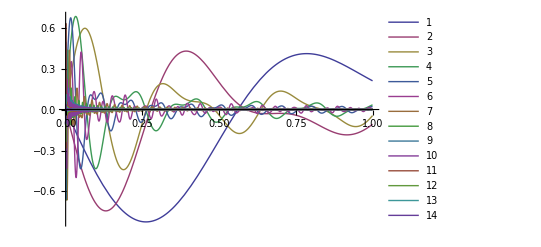

...........................................................截断的最大值

...........................................................截断的最大值列表

(0.409103 | {x→0.785398}
0.427641 | {x→0.392699}
0.594612 | {x→0.0626828}
0.681215 | {x→0.0327249}
0.671075 | {x→0.0163625}
0.421375 | {x→0.0506089}
0.433779 | {x→0.0122718}
0.433784 | {x→0.00613592}
0.0679996 | {x→0.0214757}
0.500231 | {x→0.00208577}
0.661088 | {x→0.000255656}
0.661008 | {x→0.000127826}
0.660969 | {x→0.0000639159}
0.660949 | {x→0.0000319517})

...........................................................截断的最大值图像

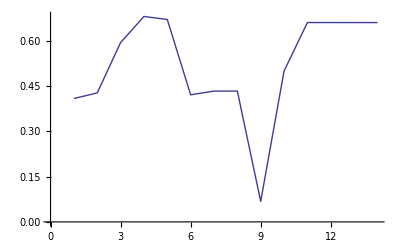

...........................................................LHS

...........................................................RHS

...........................................................LHS/RHS

{1.69231,0.565276,0.634621,3.21824,0.697695,0.709339,2.73868,0.71831,0.719826,0.720586,2.70223,0.721157,0.721252,0.7213,0.721324,3.35837}

...........................................................LHS/RHS的图像

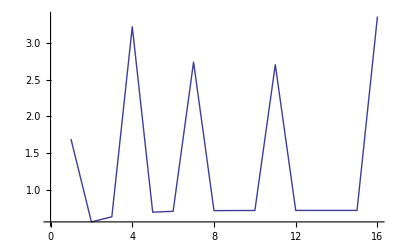

...........................................................另一波Log[Log[n]]

...........................................................a[n]已经算完

...........................................................计算5到n个的部分和

...........................................................5到n个部分和的图像

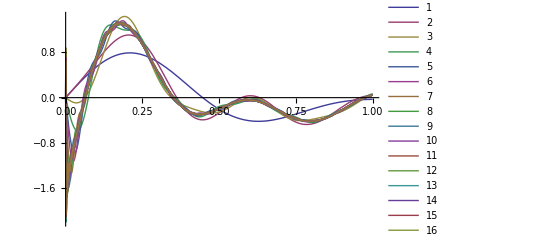

...........................................................cauchy判别

...........................................................cauchy判别图像

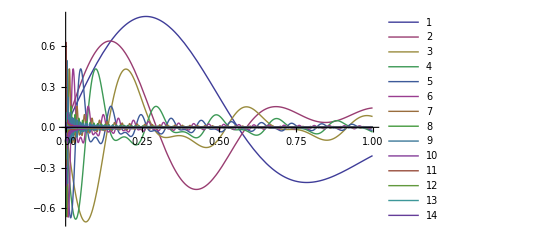

...........................................................截断的最大值

...........................................................截断的最大值列表

(0.822601 | {x→0.261799}
0.640408 | {x→0.144335}
0.432251 | {x→0.19635}
0.433402 | {x→0.0981748}
0.43369 | {x→0.0490874}
0.433762 | {x→0.0245437}
0.433779 | {x→0.0122718}
0.433784 | {x→0.00613592}
0.497182 | {x→0.00394271}
0.661246 | {x→0.000511327}
0.661088 | {x→0.000255656}
0.661008 | {x→0.000127826}
0.660969 | {x→0.0000639159}
0.660949 | {x→0.0000319517})

...........................................................截断的最大值图像

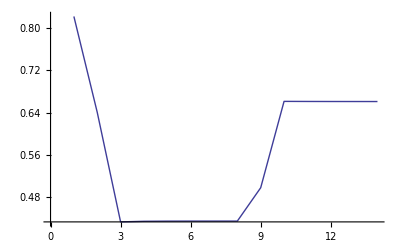

...........................................................LHS

...........................................................RHS

...........................................................LHS/RHS

{1.69231,0.565276,1.90386,0.675433,0.697695,0.709339,0.715297,0.71831,0.719826,2.54364,0.720967,0.721157,0.721252,0.7213,0.721324,0.721336}

...........................................................LHS/RHS的图像

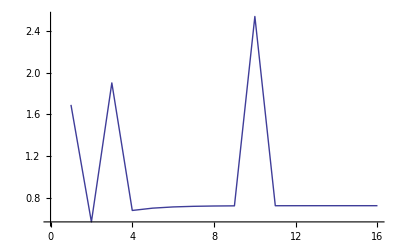

```mathematica
a[n_]:=(-1)^Floor[(Log[n])^(1/3)] 1/n;
Print["...........................................................a[n]已经算完"];
lst={10,20,30,50,80,100,150,200,250,300,400,500,800,1000,1500,2000,3000,5000,8000,10000,15000,20000,30000,50000};
Print["...........................................................计算5到n个的部分和"];
tbl=Table[∑_(k=5)^lst[[n]] (a[k]Sin[k x]),{n,Length[lst]}];
Print["...........................................................5到n个部分和的图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................cauchy判别"];
tbl=Table[∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),{n,2,15}];
Print["...........................................................cauchy判别图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................截断的最大值"];
cnvrgnclst=Table[NMaximize[{∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),0<x<1},x],{n,2,15}];
Print["...........................................................截断的最大值列表"];
cnvrgnclst//MatrixForm
Print["...........................................................截断的最大值图像"];
ListLinePlot[Map[First,cnvrgnclst]]
Print["...........................................................LHS"];
diff=Table[N[Total[Abs[Differences[Table[a[k],{k,2^m,2^(m+1)}]]]]],{m,1,16}];
Print["...........................................................RHS"];
abs=Table[N[1/2^m Total[Table[Abs[a[k]],{k,2^m,2^(m+1)}]]],{m,1,16}];
Print["...........................................................LHS/RHS"];
diff/abs
Print["...........................................................LHS/RHS的图像"];
ListLinePlot[diff/abs]
Print["...........................................................另一波(Log[n])^(2/3)"];
a[n_]:=(-1)^Floor[(Log[n])^(2/3)] 1/n;
Print["...........................................................a[n]已经算完"];
lst={10,20,30,50,80,100,150,200,250,300,400,500,800,1000,1500,2000,3000,5000,8000,10000,15000,20000,30000,50000};
Print["...........................................................计算5到n个的部分和"];
tbl=Table[∑_(k=5)^lst[[n]] (a[k]Sin[k x]),{n,Length[lst]}];
Print["...........................................................5到n个部分和的图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................cauchy判别"];
tbl=Table[∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),{n,2,15}];
Print["...........................................................cauchy判别图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................截断的最大值"];
cnvrgnclst=Table[NMaximize[{∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),0<x<1},x],{n,2,15}];
Print["...........................................................截断的最大值列表"];
cnvrgnclst//MatrixForm
Print["...........................................................截断的最大值图像"];
ListLinePlot[Map[First,cnvrgnclst]]
Print["...........................................................LHS"];
diff=Table[N[Total[Abs[Differences[Table[a[k],{k,2^m,2^(m+1)}]]]]],{m,1,16}];
Print["...........................................................RHS"];
abs=Table[N[1/2^m Total[Table[Abs[a[k]],{k,2^m,2^(m+1)}]]],{m,1,16}];
Print["...........................................................LHS/RHS"];
diff/abs
Print["...........................................................LHS/RHS的图像"];
ListLinePlot[diff/abs]
Print["...........................................................另一波Log[Log[n]]"];
a[n_]:=(-1)^Floor[Log[Log[n]]] 1/n;
Print["...........................................................a[n]已经算完"];
lst={10,20,30,50,80,100,150,200,250,300,400,500,800,1000,1500,2000,3000,5000,8000,10000,15000,20000,30000,50000};
Print["...........................................................计算5到n个的部分和"];
tbl=Table[∑_(k=5)^lst[[n]] (a[k]Sin[k x]),{n,Length[lst]}];
Print["...........................................................5到n个部分和的图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................cauchy判别"];
tbl=Table[∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),{n,2,15}];
Print["...........................................................cauchy判别图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................截断的最大值"];
cnvrgnclst=Table[NMaximize[{∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),0<x<1},x],{n,2,15}];
Print["...........................................................截断的最大值列表"];
cnvrgnclst//MatrixForm
Print["...........................................................截断的最大值图像"];
ListLinePlot[Map[First,cnvrgnclst]]
Print["...........................................................LHS"];
diff=Table[N[Total[Abs[Differences[Table[a[k],{k,2^m,2^(m+1)}]]]]],{m,1,16}];
Print["...........................................................RHS"];
abs=Table[N[1/2^m Total[Table[Abs[a[k]],{k,2^m,2^(m+1)}]]],{m,1,16}];
Print["...........................................................LHS/RHS"];
diff/abs
Print["...........................................................LHS/RHS的图像"];
ListLinePlot[diff/abs]
```

```mathematica
(Log[x])^(3/2)∨Log[x]Log[Log[x]]∨(Log[x])^(3/2)Log[Log[x]]∨√x∨√x Log[x]∨√x Log[x]^2
```

...........................................................a[n]已经算完

...........................................................计算5到n个的部分和

...........................................................5到n个部分和的图像

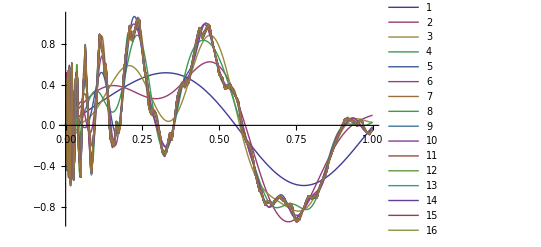

...........................................................cauchy判别

...........................................................cauchy判别图像

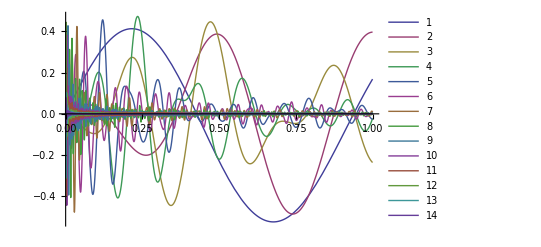

...........................................................截断的最大值

...........................................................截断的最大值列表

(0.412763 | {x→0.215795}
0.39634 | {x→1.}
0.446127 | {x→0.471782}
0.472198 | {x→0.234522}
0.455731 | {x→0.120651}
0.376117 | {x→0.0648971}
0.424095 | {x→0.0367218}
0.36669 | {x→0.0206967}
0.427182 | {x→0.00768264}
0.301842 | {x→0.00273464}
0.426421 | {x→0.00187303}
0.446874 | {x→0.00123602}
0.362982 | {x→0.000521649}
0.250135 | {x→0.000221607})

...........................................................截断的最大值图像

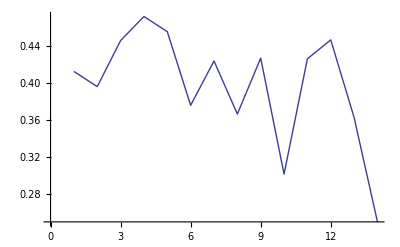

...........................................................LHS

...........................................................RHS

...........................................................LHS/RHS

{1.69231,2.37416,4.4532,4.49442,4.61129,4.84476,6.70372,4.59989,6.8065,6.42848,4.83413,9.16612,6.4551,6.76049,7.20967,9.39073}

...........................................................LHS/RHS的图像

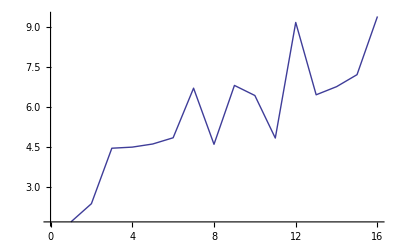

...........................................................另一波Log[x]Log[Log[x]]

...........................................................a[n]已经算完

...........................................................计算5到n个的部分和

...........................................................5到n个部分和的图像

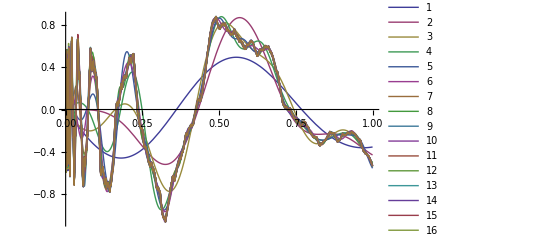

...........................................................cauchy判别

...........................................................cauchy判别图像

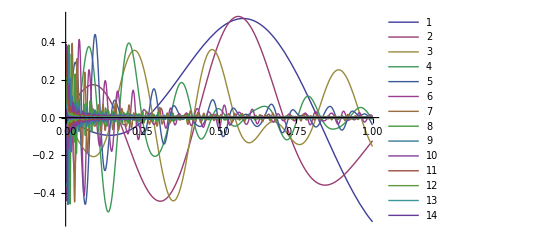

...........................................................截断的最大值

...........................................................截断的最大值列表

(0.524452 | {x→0.578507}
0.535273 | {x→0.562464}
0.360103 | {x→0.477218}
0.394422 | {x→0.206194}
0.439994 | {x→0.0959236}
0.413985 | {x→0.0443551}
0.393727 | {x→0.0211127}
0.384747 | {x→0.0104118}
0.380921 | {x→0.0052948}
0.385782 | {x→0.00275135}
0.398482 | {x→0.00144561}
0.191345 | {x→0.00131819}
0.467413 | {x→0.000430772}
0.462649 | {x→0.000232592})

...........................................................截断的最大值图像

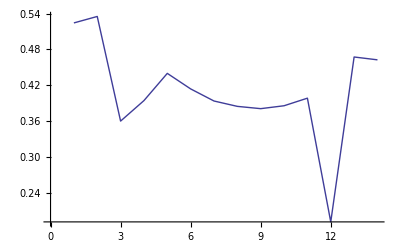

...........................................................LHS

...........................................................RHS

...........................................................LHS/RHS

{1.69231,2.07268,2.48079,4.62082,2.72735,5.29497,4.94313,4.7706,4.72742,4.78084,4.91891,5.13511,6.89888,4.48416,4.85919,6.78661}

...........................................................LHS/RHS的图像

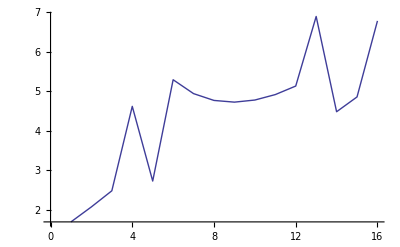

...........................................................另一波(Log[x])^(3/2)Log[Log[x]]

...........................................................a[n]已经算完

...........................................................计算5到n个的部分和

...........................................................5到n个部分和的图像

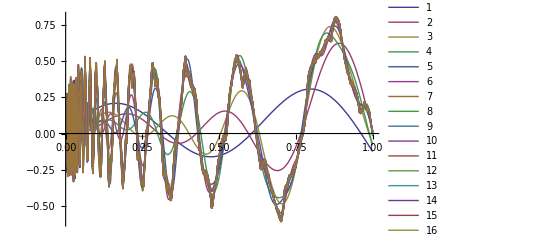

...........................................................cauchy判别

...........................................................cauchy判别图像

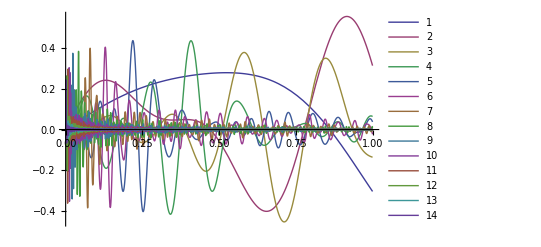

...........................................................截断的最大值

...........................................................截断的最大值列表

(0.279682 | {x→0.523599}
0.556497 | {x→0.916298}
0.379283 | {x→0.581615}
0.436842 | {x→0.408361}
0.437569 | {x→0.219013}
0.40542 | {x→0.129141}
0.400466 | {x→0.0797682}
0.386694 | {x→0.0420203}
0.377884 | {x→0.0233629}
0.334236 | {x→0.011483}
0.34268 | {x→0.00696179}
0.315143 | {x→0.00373008}
0.325935 | {x→0.00180842}
0.257335 | {x→0.000914237})

...........................................................截断的最大值图像

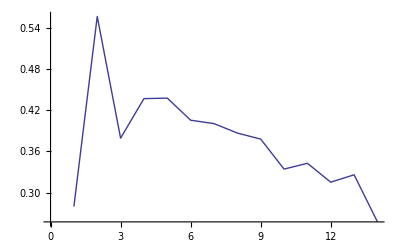

...........................................................LHS

...........................................................RHS

...........................................................LHS/RHS

{1.69231,3.20323,3.93135,7.99376,7.97816,8.70195,13.1994,12.9713,15.0762,15.225,17.7028,19.6157,19.4734,21.6249,21.691,24.0254}

...........................................................LHS/RHS的图像

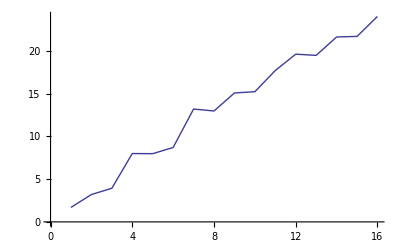

...........................................................另一波√x

...........................................................a[n]已经算完

...........................................................计算5到n个的部分和

...........................................................5到n个部分和的图像

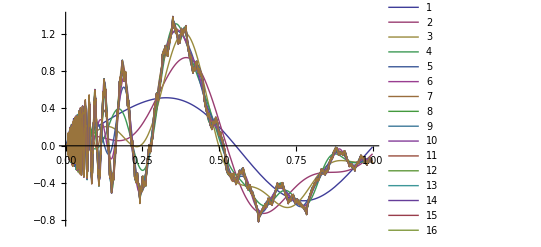

...........................................................cauchy判别

...........................................................cauchy判别图像

-Graphics-

...........................................................截断的最大值

...........................................................截断的最大值列表

(0.822601 | {x→0.261799}
0.427641 | {x→0.392699}
0.43545 | {x→0.388624}
0.394453 | {x→0.189361}
0.370789 | {x→0.124016}
0.38365 | {x→0.127724}
0.440407 | {x→0.0779757}
0.3798 | {x→0.055574}
0.31345 | {x→0.0431173}
0.275218 | {x→0.0278248}
0.251343 | {x→0.021723}
0.212671 | {x→0.0150313}
0.165738 | {x→0.00932743}
0.130601 | {x→0.00725375})

...........................................................截断的最大值图像

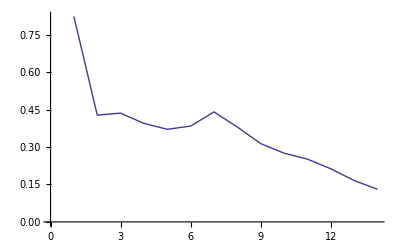

...........................................................LHS

...........................................................RHS

...........................................................LHS/RHS

{1.38462,0.565276,4.16029,2.40454,6.39633,6.26786,10.3525,12.5977,20.8727,26.6635,38.9549,53.3466,77.9465,108.142,153.034,216.29}

...........................................................LHS/RHS的图像

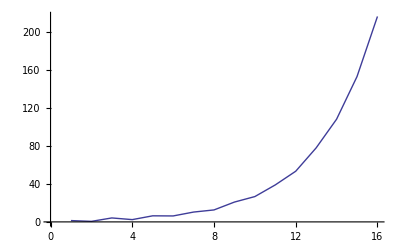

...........................................................另一波√xLog[x]

...........................................................a[n]已经算完

...........................................................计算5到n个的部分和

...........................................................5到n个部分和的图像

-Graphics-

...........................................................cauchy判别

...........................................................cauchy判别图像

-Graphics-

...........................................................截断的最大值

...........................................................截断的最大值列表

(0.318095 | {x→0.581958}
0.124909 | {x→0.392699}
0.139309 | {x→0.739566}
0.0786688 | {x→0.81707}
0.169676 | {x→1.}
0.223156 | {x→0.864926}
0.193482 | {x→0.624967}
0.170673 | {x→0.536521}
0.127643 | {x→0.417395}
0.0955189 | {x→0.262847}
0.0896425 | {x→0.242986}
0.0118008 | {x→0.550512}
0.00494293 | {x→0.993921}
0.0381953 | {x→0.0880878})

...........................................................截断的最大值图像

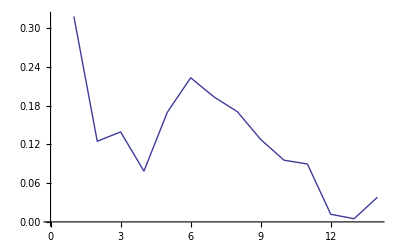

...........................................................LHS

...........................................................RHS

...........................................................LHS/RHS

{2.61538,5.17362,10.7994,15.2979,27.7895,42.4299,69.3796,107.695,162.613,252.268,379.977,575.663,868.548,1301.5,1946.51,2902.93}

...........................................................LHS/RHS的图像

-Graphics-

...........................................................另一波√xLog[x]^2

...........................................................a[n]已经算完

...........................................................计算5到n个的部分和

...........................................................5到n个部分和的图像

-Graphics-

...........................................................cauchy判别

...........................................................cauchy判别图像

-Graphics-

...........................................................截断的最大值

...........................................................截断的最大值列表

(0.64508 | {x→1.}
0.556497 | {x→0.916298}
0.446785 | {x→0.973629}
0.354177 | {x→0.629022}
0.403857 | {x→0.214595}
0.15624 | {x→0.937946}
0.0473501 | {x→1.}
0.0369867 | {x→0.49725}
0.0159387 | {x→0.34262}
0.00655282 | {x→0.999261}
0.0124759 | {x→0.0860541}
0.00612531 | {x→0.940698}
0.00355665 | {x→0.958348}
0.00317804 | {x→0.0876427})

...........................................................截断的最大值图像

-Graphics-

...........................................................LHS

...........................................................RHS

...........................................................LHS/RHS

{1.38462,1.85734,3.93135,10.4123,14.9885,8.63756,58.3179,237.81,719.315,1878.02,3634.59,5914.27,9526.78,15228.,24160.2,38090.5}

...........................................................LHS/RHS的图像

-Graphics-

```mathematica
a[n_]:=(-1)^Floor[(Log[n])^(3/2)] 1/n;
Print["...........................................................a[n]已经算完"];
lst={10,20,30,50,80,100,150,200,250,300,400,500,800,1000,1500,2000,3000,5000,8000,10000,15000,20000,30000,50000};
Print["...........................................................计算5到n个的部分和"];
tbl=Table[∑_(k=5)^lst[[n]] (a[k]Sin[k x]),{n,Length[lst]}];
Print["...........................................................5到n个部分和的图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................cauchy判别"];
tbl=Table[∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),{n,2,15}];
Print["...........................................................cauchy判别图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................截断的最大值"];
cnvrgnclst=Table[NMaximize[{∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),0<x<1},x],{n,2,15}];
Print["...........................................................截断的最大值列表"];
cnvrgnclst//MatrixForm
Print["...........................................................截断的最大值图像"];
ListLinePlot[Map[First,cnvrgnclst]]
Print["...........................................................LHS"];
diff=Table[N[Total[Abs[Differences[Table[a[k],{k,2^m,2^(m+1)}]]]]],{m,1,16}];
Print["...........................................................RHS"];
abs=Table[N[1/2^m Total[Table[Abs[a[k]],{k,2^m,2^(m+1)}]]],{m,1,16}];
Print["...........................................................LHS/RHS"];
diff/abs
Print["...........................................................LHS/RHS的图像"];
ListLinePlot[diff/abs]
Print["...........................................................另一波Log[x]Log[Log[x]]"];
a[n_]:=(-1)^Floor[Log[n]Log[Log[n]]] 1/n;
Print["...........................................................a[n]已经算完"];
lst={10,20,30,50,80,100,150,200,250,300,400,500,800,1000,1500,2000,3000,5000,8000,10000,15000,20000,30000,50000};
Print["...........................................................计算5到n个的部分和"];
tbl=Table[∑_(k=5)^lst[[n]] (a[k]Sin[k x]),{n,Length[lst]}];
Print["...........................................................5到n个部分和的图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................cauchy判别"];
tbl=Table[∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),{n,2,15}];
Print["...........................................................cauchy判别图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................截断的最大值"];
cnvrgnclst=Table[NMaximize[{∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),0<x<1},x],{n,2,15}];
Print["...........................................................截断的最大值列表"];
cnvrgnclst//MatrixForm
Print["...........................................................截断的最大值图像"];
ListLinePlot[Map[First,cnvrgnclst]]
Print["...........................................................LHS"];
diff=Table[N[Total[Abs[Differences[Table[a[k],{k,2^m,2^(m+1)}]]]]],{m,1,16}];
Print["...........................................................RHS"];
abs=Table[N[1/2^m Total[Table[Abs[a[k]],{k,2^m,2^(m+1)}]]],{m,1,16}];
Print["...........................................................LHS/RHS"];
diff/abs
Print["...........................................................LHS/RHS的图像"];
ListLinePlot[diff/abs]
Print["...........................................................另一波(Log[x])^(3/2)Log[Log[x]]"];
a[n_]:=(-1)^Floor[(Log[n])^(3/2)Log[Log[n]]] 1/n;
Print["...........................................................a[n]已经算完"];
lst={10,20,30,50,80,100,150,200,250,300,400,500,800,1000,1500,2000,3000,5000,8000,10000,15000,20000,30000,50000};
Print["...........................................................计算5到n个的部分和"];
tbl=Table[∑_(k=5)^lst[[n]] (a[k]Sin[k x]),{n,Length[lst]}];
Print["...........................................................5到n个部分和的图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................cauchy判别"];
tbl=Table[∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),{n,2,15}];
Print["...........................................................cauchy判别图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................截断的最大值"];
cnvrgnclst=Table[NMaximize[{∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),0<x<1},x],{n,2,15}];
Print["...........................................................截断的最大值列表"];
cnvrgnclst//MatrixForm
Print["...........................................................截断的最大值图像"];
ListLinePlot[Map[First,cnvrgnclst]]
Print["...........................................................LHS"];
diff=Table[N[Total[Abs[Differences[Table[a[k],{k,2^m,2^(m+1)}]]]]],{m,1,16}];
Print["...........................................................RHS"];
abs=Table[N[1/2^m Total[Table[Abs[a[k]],{k,2^m,2^(m+1)}]]],{m,1,16}];
Print["...........................................................LHS/RHS"];
diff/abs
Print["...........................................................LHS/RHS的图像"];
ListLinePlot[diff/abs]
Print["...........................................................另一波√x"];
a[n_]:=(-1)^Floor[√n] 1/n;
Print["...........................................................a[n]已经算完"];
lst={10,20,30,50,80,100,150,200,250,300,400,500,800,1000,1500,2000,3000,5000,8000,10000,15000,20000,30000,50000};
Print["...........................................................计算5到n个的部分和"];
tbl=Table[∑_(k=5)^lst[[n]] (a[k]Sin[k x]),{n,Length[lst]}];
Print["...........................................................5到n个部分和的图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................cauchy判别"];
tbl=Table[∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),{n,2,15}];
Print["...........................................................cauchy判别图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................截断的最大值"];
cnvrgnclst=Table[NMaximize[{∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),0<x<1},x],{n,2,15}];
Print["...........................................................截断的最大值列表"];
cnvrgnclst//MatrixForm
Print["...........................................................截断的最大值图像"];
ListLinePlot[Map[First,cnvrgnclst]]
Print["...........................................................LHS"];
diff=Table[N[Total[Abs[Differences[Table[a[k],{k,2^m,2^(m+1)}]]]]],{m,1,16}];
Print["...........................................................RHS"];
abs=Table[N[1/2^m Total[Table[Abs[a[k]],{k,2^m,2^(m+1)}]]],{m,1,16}];
Print["...........................................................LHS/RHS"];
diff/abs
Print["...........................................................LHS/RHS的图像"];
ListLinePlot[diff/abs]
Print["...........................................................另一波√xLog[x]"];
a[n_]:=(-1)^Floor[√n Log[n]] 1/n;
Print["...........................................................a[n]已经算完"];
lst={10,20,30,50,80,100,150,200,250,300,400,500,800,1000,1500,2000,3000,5000,8000,10000,15000,20000,30000,50000};
Print["...........................................................计算5到n个的部分和"];
tbl=Table[∑_(k=5)^lst[[n]] (a[k]Sin[k x]),{n,Length[lst]}];
Print["...........................................................5到n个部分和的图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................cauchy判别"];
tbl=Table[∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),{n,2,15}];
Print["...........................................................cauchy判别图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................截断的最大值"];
cnvrgnclst=Table[NMaximize[{∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),0<x<1},x],{n,2,15}];
Print["...........................................................截断的最大值列表"];
cnvrgnclst//MatrixForm
Print["...........................................................截断的最大值图像"];
ListLinePlot[Map[First,cnvrgnclst]]
Print["...........................................................LHS"];
diff=Table[N[Total[Abs[Differences[Table[a[k],{k,2^m,2^(m+1)}]]]]],{m,1,16}];
Print["...........................................................RHS"];
abs=Table[N[1/2^m Total[Table[Abs[a[k]],{k,2^m,2^(m+1)}]]],{m,1,16}];
Print["...........................................................LHS/RHS"];
diff/abs
Print["...........................................................LHS/RHS的图像"];
ListLinePlot[diff/abs]
Print["...........................................................另一波√xLog[x]^2"];
a[n_]:=(-1)^Floor[√n Log[n]^2] 1/n;
Print["...........................................................a[n]已经算完"];
lst={10,20,30,50,80,100,150,200,250,300,400,500,800,1000,1500,2000,3000,5000,8000,10000,15000,20000,30000,50000};
Print["...........................................................计算5到n个的部分和"];
tbl=Table[∑_(k=5)^lst[[n]] (a[k]Sin[k x]),{n,Length[lst]}];
Print["...........................................................5到n个部分和的图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................cauchy判别"];
tbl=Table[∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),{n,2,15}];
Print["...........................................................cauchy判别图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................截断的最大值"];
cnvrgnclst=Table[NMaximize[{∑_(k=2^n)^(2^(n+1)) (a[k]Sin[k x]),0<x<1},x],{n,2,15}];
Print["...........................................................截断的最大值列表"];
cnvrgnclst//MatrixForm
Print["...........................................................截断的最大值图像"];
ListLinePlot[Map[First,cnvrgnclst]]
Print["...........................................................LHS"];
diff=Table[N[Total[Abs[Differences[Table[a[k],{k,2^m,2^(m+1)}]]]]],{m,1,16}];
Print["...........................................................RHS"];
abs=Table[N[1/2^m Total[Table[Abs[a[k]],{k,2^m,2^(m+1)}]]],{m,1,16}];
Print["...........................................................LHS/RHS"];
diff/abs
Print["...........................................................LHS/RHS的图像"];
ListLinePlot[diff/abs]
```

If ∑_(n=1)^∞ a_n sin nx  converges uniformly on [0,2π], and ∑_(k=n)^(2n)|Δa_k|≤M/n∑_(k=n/λ)^λn|a_k|, then OverBar[lim]_(n→∞)n a_n=0 or ∞